```mathematica
f[x_]:= 1/(x^8+1)
```

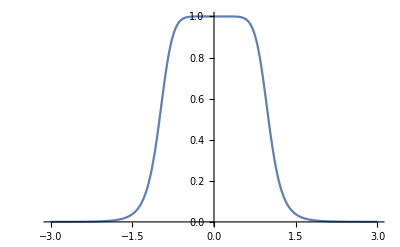

```mathematica
Plot[f[x], {x,-3,3}]
```

```mathematica
$Assumptions={a∈Reals};
```

```mathematica
∫_(a-1)^(a+1) 1/(1+x^8)ⅆx
```

```mathematica
1/8 (-2 ArcTan[Sec[π/8] (-1+a-Sin[π/8])] Cos[π/8]-2 ArcTan[Sec[π/8] (-1+a+Sin[π/8])] Cos[π/8]+2 ArcTan[Sec[π/8] (1+a+Sin[π/8])] Cos[π/8]+2 ArcTan[(1+a) Sec[π/8]-Tan[π/8]] Cos[π/8]-Cos[π/8] Log[2+2 a+a^2-2 Cos[π/8]-2 a Cos[π/8]]-f]]+Cos[π/8] Log[2+2 a+a^2+2 Cos[π/8]+2 a Cos[π/8]]+Cos[π/8] Log[a^2+2 (1+Cos[π/8])-2 a (1+Cos[π/8])]+2 ArcTan[(1-a+Cos[π/8]) Csc[π/8]] Sin[π/8]-2 ArcTan[(-1+a+Cos[π/8]) Csc[π/8]] Sin[π/8]+2 ArcTan[(1+a+Cos[π/8]) Csc[π/8]] Sin[π/8]-2 ArcTan[Cot[π/8]-(1+a) Csc[π/8]] Sin[π/8]-Log[2+a^2+2 a (-1+Sin[π/8])-2 Sin[π/8]] Sin[π/8]-Log[2+2 a+a^2-2 Sin[π/8]-2 a Sin[π/8]] Sin[π/8]+Log[2+2 a+a^2+2 Sin[π/8]+2 a Sin[π/8]] Sin[π/8]+Log[a^2+2 (1+Sin[π/8])-2 a (1+Sin[π/8])] Sin[π/8])
```

```mathematica
ℐ[a_]:= 1/8 (-2 ArcTan[Sec[π/8] (-1+a-Sin[π/8])] Cos[π/8]-2 ArcTan[Sec[π/8] (-1+a+Sin[π/8])] Cos[π/8]+2 ArcTan[Sec[π/8] (1+a+Sin[π/8])] Cos[π/8]+2 ArcTan[(1+a) Sec[π/8]-Tan[π/8]] Cos[π/8]-Cos[π/8] Log[2+2 a+a^2-2 Cos[π/8]-2 a Cos[π/8]]-Cos[π/8] Log[2-2 a+a^2-2 Cos[π/8]+2 a Cos[π/8]]+Cos[π/8] Log[2+2 a+a^2+2 Cos[π/8]+2 a Cos[π/8]]+Cos[π/8] Log[a^2+2 (1+Cos[π/8])-2 a (1+Cos[π/8])]+2 ArcTan[(1-a+Cos[π/8]) Csc[π/8]] Sin[π/8]-2 ArcTan[(-1+a+Cos[π/8]) Csc[π/8]] Sin[π/8]+2 ArcTan[(1+a+Cos[π/8]) Csc[π/8]] Sin[π/8]-2 ArcTan[Cot[π/8]-(1+a) Csc[π/8]] Sin[π/8]-Log[2+a^2+2 a (-1+Sin[π/8])-2 Sin[π/8]] Sin[π/8]-Log[2+2 a+a^2-2 Sin[π/8]-2 a Sin[π/8]] Sin[π/8]+Log[2+2 a+a^2+2 Sin[π/8]+2 a Sin[π/8]] Sin[π/8]+Log[a^2+2 (1+Sin[π/8])-2 a (1+Sin[π/8])] Sin[π/8]);
```

```mathematica
Maximize[ℐ[a], a]
```

{1/8 (-2 ArcTan[Sec[π/8] (-1-Sin[π/8])] Cos[π/8]-2 ArcTan[Sec[π/8] (-1+Sin[π/8])] Cos[π/8]+2 ArcTan[Sec[π/8] (1+Sin[π/8])] Cos[π/8]+2 ArcTan[Sec[π/8]-Tan[π/8]] Cos[π/8]-2 Cos[π/8] Log[2-2 Cos[π/8]]+Cos[π/8] Log[2 (1+Cos[π/8])]+Cos[π/8] Log[2+2 Cos[π/8]]-2 ArcTan[Cot[π/8]-Csc[π/8]] Sin[π/8]-2 ArcTan[(-1+Cos[π/8]) Csc[π/8]] Sin[π/8]+4 ArcTan[(1+Cos[π/8]) Csc[π/8]] Sin[π/8]-2 Log[2-2 Sin[π/8]] Sin[π/8]+Log[2 (1+Sin[π/8])] Sin[π/8]+Log[2+2 Sin[π/8]] Sin[π/8]),{a→0}}

```mathematica
First[%]/.a-> 0
```

1/8 (-2 ArcTan[Sec[π/8] (-1-Sin[π/8])] Cos[π/8]-2 ArcTan[Sec[π/8] (-1+Sin[π/8])] Cos[π/8]+2 ArcTan[Sec[π/8] (1+Sin[π/8])] Cos[π/8]+2 ArcTan[Sec[π/8]-Tan[π/8]] Cos[π/8]-2 Cos[π/8] Log[2-2 Cos[π/8]]+Cos[π/8] Log[2 (1+Cos[π/8])]+Cos[π/8] Log[2+2 Cos[π/8]]-2 ArcTan[Cot[π/8]-Csc[π/8]] Sin[π/8]-2 ArcTan[(-1+Cos[π/8]) Csc[π/8]] Sin[π/8]+4 ArcTan[(1+Cos[π/8]) Csc[π/8]] Sin[π/8]-2 Log[2-2 Sin[π/8]] Sin[π/8]+Log[2 (1+Sin[π/8])] Sin[π/8]+Log[2+2 Sin[π/8]] Sin[π/8])

```mathematica
%//N
```

1.8493